2.71828

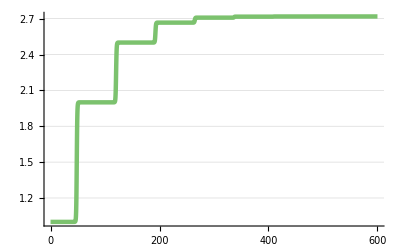

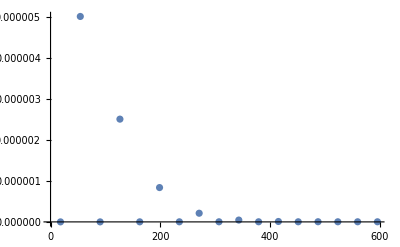

```mathematica
Get[NotebookDirectory[]<>"/euler.m"]
rsys=EulerRsys[];
tmax=600;
sol=SimulateRxnsys[ExpandRsys[rsys], tmax];
EvaluateRxnAtPoint[sol,e,tmax]
PlotForPaper[Evaluate[{e[t]}/.sol], tmax, 200]
errorMap=EvaluateError[rsys, tmax];
eulerErrorList=errorMap[e]/.{resultMap_}:>{resultMap["time"],resultMap["error"]};
ListPlot[eulerErrorList,PlotRange->{0,All},Ticks->{Range[0,tmax,200],Automatic}]
```